### NALOGA 1

#### Primer A

```mathematica
izraz = (x^5 - 2x^2 + 3x +4) / (x^5 - 2x -1)
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
izraz /.  x-> 1
```

-3

```mathematica
ReplaceAll[izraz, x -> 1]
```

-3

```mathematica
izraz /. x -> {1, 2, 3, 4}
```

{-3,34/27,119/118,144/145}

```mathematica
izraz /. {{x -> 1}, {x -> 2}, {x -> 3}, {x -> 4}}
```

{-3,34/27,119/118,144/145}

### Primer B

```mathematica
f[x_] := (x^5 - 2x^2 + 3x +4) / (x^5 - 2x -1)
f[1]
```

-3

```mathematica
f[2]
```

34/27

```mathematica
f[3]
```

119/118

```mathematica
f[4]
```

144/145

```mathematica
Table[f[i], {i, 1, 4}]
```

{-3,34/27,119/118,144/145}

### NALOGA 2

```mathematica
sez = {10, 20, 30, 40, 50, 60, 70}

Take[sez, 3]
Take[sez, -2]
```

{10,20,30,40,50,60,70}

{10,20,30}

```mathematica
{60,70}
Part[sez, {2, 3, 5}]
Drop[sez, {4, 5}]
```

{60,70}

{20,30,50}

{10,20,30,60,70}

### 3. naloga

```mathematica
ClearAll[x, a]
sez = {x^6, x^2, a}
```

```mathematica
{x^6,x^2,a}
sez /. x -> 3
```

{x^6,x^2,a}

{729,9,a}

```mathematica
sez /. x -> x^2
```

{x^12,x^4,a}

```mathematica
sez /. x^2 -> x
```

{x^6,x,a}

```mathematica
sez /. x -> {1, 2, 3}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez /. {x -> 3, a -> x}
```

{729,9,x}

```mathematica
ReplaceAll[sez, {x -> 3, a -> x}]
```

{729,9,x}

```mathematica
ReplaceRepeated[sez, {x -> 3, a -> x}]
```

{729,9,3}

```mathematica
{sez /. x -> 1, sez /. x -> 2, sez /. x -> 3}
```

{{1,1,a},{64,4,a},{729,9,a}}

```mathematica
Table[sez /. x -> i, {i, 1, 3}]
```

{{1,1,a},{64,4,a},{729,9,a}}

```mathematica
ClearAll[f]
Map[f, {1, 2, a}]
```

{f[1],f[2],f[a]}

### Naloga 4

```mathematica
D[x^5 + 4x^3 - 9, x] /. {{x -> 1}, {x -> 5} }
```

{17,3425}

```mathematica
D[E^(x^(1/4)), x] /. {{x -> 1}, {x -> 2}}
```

{ⅇ/4,(ⅇ^(2^(1/4)))/(4 2^(3/4))}

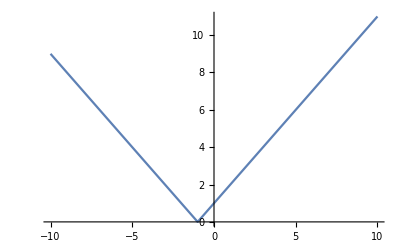

```mathematica
Plot[Abs[x +1], {x, -10, 10}]
```

```mathematica
FullSimplify[D[Abs[x +1], x], Element[x, Reals] && x ≠
```

```mathematica
Sign[-1]
```

-1

```mathematica
ClearAll[a, b, x]
D[a x^2 + 3b, x] /. {{x -> 1}, {x -> 2}}
```

{2 a,4 a}

### Naloga 5

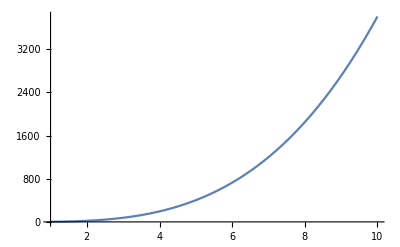

5

402.359

```mathematica
f[x_] := x^3 * Log[4x + 5]
Plot[f[x], {x, 1, 10}]

x0 = 5
f[x0] // N
```

```mathematica
k = D[f[x], x] /. x -> x0
k // N
```

20+75 Log[25]

261.416

```mathematica
ClearAll[x, y, b]
n /. Solve[y == k x + n /. {x -> x0, y -> f[x0]}, n ]
```

{-50 (2+5 Log[25])}